## Second-Order Runge-Kutta — Mass on a Spring

## Done in class, January 29, 2025

This is a third notebook for you to finish in-class. First let’s recap and improve the last notebook which had a sinusoidal acceleration hard-coded into it.

### Sinusoidal Acceleration Notebook — Recap

#### Problem Description

Our final version of the sinusoidal acceleration problem had F=-10sin 2t and m=5. With t_initial=0.0 and t_final=3π, we had three full periods of the sine function, and we had 72 time steps:

```mathematica
force[t_]:=-10 Sin[2t]
m=5;
a[t_] := force[t]/m;
tInitial = 0.0;
tFinal = 3Pi; 
steps = 72;
deltaT = (tFinal - tInitial)/steps;
```

#### Initial Conditions

We chose x_initial=0 and v_initial=1.0.

```mathematica
xInitial=0.0;
vInitial=1.0;
aInitial=0.0;
initialConditions={tInitial,xInitial,vInitial, aInitial};
```

#### Update Procedure — Theory

For the sinusoidal acceleration notebook, the theory we implemented updated all three of time, position, and velocity as follows:

t_(i+1)=t_i+Δt

v(t_(i+1))=v(t_i)+a(t_i+Δt/2)·Δt

x(t_(i+1))=x(t_i)+(v(t_i)+v(t_(i+1)))·Δt/2

#### Update Procedure — Implementation

Below is an implementation of that is a bit better than the one we did in class. I added some parenthesis and within those parenthesis I am able to define variables before returning a result. This makes the implementation more readable.

```mathematica
procedure[cc_]:=(
(* Extract time, position, and velocity from the list. *)
curTime=cc[[1]];
curPosition=cc[[2]];
curVelocity=cc[[3]];
(* Implement the three equations in the theory above. *)
newTime=curTime+deltaT;
newVelocity=curVelocity+a[curTime+deltaT/2] deltaT;
newPosition=curPosition+(curVelocity+newVelocity) deltaT / 2;
(* We don't need newAcceleration for the procedure, but it is nice to show acceleration as a plot too,
so tabulate it too. *)
newAcceleration=a[newTime];
{newTime,newPosition,newVelocity, newAcceleration}
)
```

I hope you agree that it has become much clearer what each line of procedure does, and also made it less likely that we will have typos in extracting the time, the position, and the velocity from the list.

#### Plotting the Sinusoidal Acceleration Results

We nested the procedure 72 times:

```mathematica
results=NestList[procedure,initialConditions, steps];
```

We transposed the results to make it easier to take parts of them:

```mathematica
resultsTransposed=Transpose[results];
```

Then we plotted them.

```mathematica
accelerationPlot=ListLinePlot[Transpose[resultsTransposed[[{1,4}]]]];
velocityPlot = ListLinePlot[Transpose[resultsTransposed[[{1,3}]]]];
positionPlot = ListLinePlot[Transpose[resultsTransposed[[{1,2}]]]];
```

Usually we display those as a column sot that the time axes line up vertically, but to save space, I’ll display them as a row:

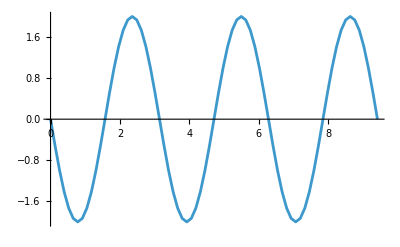
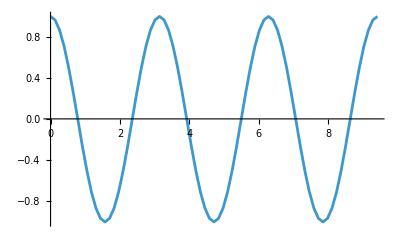
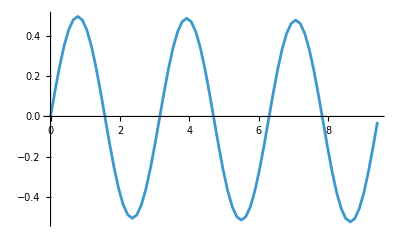

```mathematica
Row[{accelerationPlot, velocityPlot,positionPlot}]
```

### Mass on a Spring

Everything up to this point in this notebook was review (with a few mild improvements) of stuff we did in the last class. Finally we get to the new stuff.

#### Problem Description

```mathematica
springForce[x_]:=-20 x (* notice how incredibly different this is! *)
mass=5;
a[x_] := springForce[x]/mass;
tInitial = 0;
tFinal = 3Pi; 
steps = 72;
deltaT = (tFinal - tInitial)/steps;
```

#### Initial Conditions

Let’s stretch this spring to x_initial=25 and let it go with no initial velocity, so v_initial=0.0.

```mathematica
xInitial=25.0;
vInitial=0.0;
aInitial=a[xInitial];
initialConditions={tInitial,xInitial,vInitial, aInitial};
```

#### Second-Order Runge-Kutta — Theory — Summary

Because the force now depends on the position instead of the time, we had to revisit our procedure, and the procedure we ended up with is called Second-Order Runge-Kutta:

t_(i+1)=t_i+Δt

x^*(t_(i+1))=x(t_i)+v(t_i)Δt

v(t_(i+1))=v(t_i)+(a(x(t_i))+a(x^*(t_(i+1))))·Δt/2

x(t_(i+1))=x(t_i)+(v(t_i)+v(t_(i+1)))·Δt/2

The above four equations are a self-contained summary of what was in our last theory handout, and they are what you will be implementing in the next section.

#### Second-Order Runge-Kutta — Implementation

```mathematica
rungeKutta2[cc_]:=(
(* Extract time, position, and velocity from the list. *)
curTime=cc[[1]];
(* Implement the four equations in the theory above. *)
(* So we can display it easily, tabulate acceleration too. *)
newAcceleration=a[newPosition];
{newTime, newPosition, newVelocity, newAcceleration}
)
```

#### Displaying the Mass on a Spring Results

Nest the procedure 72 times and then transpose the results and produce three plots:

```mathematica
rk2Results=NestList[rungeKutta2,initialConditions, steps];rk2ResultsTransposed=Transpose[rk2Results];
accelerationPlot=ListPlot[Transpose[rk2ResultsTransposed[[{1,4}]]]];
velocityPlot = ListPlot[Transpose[rk2ResultsTransposed[[{1,3}]]]];
positionPlot = ListPlot[Transpose[rk2ResultsTransposed[[{1,2}]]]];
Column[{accelerationPlot,velocityPlot,positionPlot}]
```

#### Conclusion / Commentary

The plots above look mighty similar to the plots we got last time, but now we are getting our results completely differently! Our idealized spring just obeys F(x)=-20x. Nowhere did we put sines or cosines into the problem! Oscillation emerged naturally.

It happens that the position and acceleration are following a cosine function, and the velocity is following a sine function. With different initial conditions you can switch these or make any mixture. Here is a video showing the bizarre fact that a mass on a spring has some resemblance to a particle moving in a circle: https://youtu.be/ZlleypTKfGY. I happen to know, using calculus, that the exact solution for the mass on a spring with the initial conditions that we chose is:

a(t)=-100cos 2t
v(t)=-50 sin 2t
x(t)=25 cos 2t

You can see by studying the graphs that Mathematica has done a darned good job of using Second-Order Runge-Kutte — which to be sure is an approximate method — to get close to the exact solution, and if you changed the number of steps to 720, or 7200, Mathematica would get even closer to the exact solution.

Soon we will be using Mathematica to solve problems that cannot be solved exactly using calculus!